# HW 6 - ASTR510

## Daniel George

## Q1

## Taylor expansions

### q(t+dt)

```mathematica
TE1=Series[q[t+dt],{dt,0,3}]
```

q[t]+q'[t] dt+1/2 q''[t] dt^2+1/6 q^(3)[t] dt^3+O[dt]^4

### q(t+1/2dt)

```mathematica
TE2=Series[q[t+1/2dt],{dt,0,3}]
```

q[t]+1/2 q'[t] dt+1/8 q''[t] dt^2+1/48 q^(3)[t] dt^3+O[dt]^4

## Defining linear operators A and B

```mathematica
A[x_+y_]=A[x]+A[y]; A[c_ q_[t_]]=c A[q[t]];A[0]=0;
B[x_+y_]=B[x]+B[y]; B[c_ q_[t_]]=c B[q[t]]; B[0]=0;
```

## Correct value of q after time dt

```mathematica
eqC=q[t+dt]->TE1//.Derivative[n_][q][t]->A[Derivative[n-1][q][t]]+B[Derivative[n-1][q][t]]
```

q[dt+t]→q[t]+(A[q[t]]+B[q[t]]) dt+1/2 (A[A[q[t]]]+A[B[q[t]]]+B[A[q[t]]]+B[B[q[t]]]) dt^2+1/6 (A[A[A[q[t]]]]+A[A[B[q[t]]]]+A[B[A[q[t]]]]+A[B[B[q[t]]]]+B[A[A[q[t]]]]+B[A[B[q[t]]]]+B[B[A[q[t]]]]+B[B[B[q[t]]]]) dt^3+O[dt]^4

a)

## Computing value using Godunov method

### Replacing derivatives in Taylor expansion using operator B

```mathematica
step1G=TE1//.Derivative[n_][q][t]->B[Derivative[n-1][q][t]]//Normal
```

1/6 dt^3 B[B[B[q[t]]]]+1/2 dt^2 B[B[q[t]]]+dt B[q[t]]+q[t]

### Substituting this expression for q(t) in the Taylor expansion having operator A

```mathematica
step2G=(step1G/.{B->A})/.q[t]->step1G//Simplify//Normal[#+O[dt]^4]&
```

1/6 dt^3 (A[A[A[q[t]]]]+3 A[A[B[q[t]]]]+3 A[B[B[q[t]]]]+B[B[B[q[t]]]])+1/2 dt^2 (A[A[q[t]]]+2 A[B[q[t]]]+B[B[q[t]]])+dt (A[q[t]]+B[q[t]])+q[t]

### Final value of q after time dt using Godunov method

```mathematica
eqG=q[t+dt]->step2G+O[dt]^4
```

q[dt+t]→q[t]+(A[q[t]]+B[q[t]]) dt+1/2 (A[A[q[t]]]+2 A[B[q[t]]]+B[B[q[t]]]) dt^2+1/6 (A[A[A[q[t]]]]+3 A[A[B[q[t]]]]+3 A[B[B[q[t]]]]+B[B[B[q[t]]]]) dt^3+O[dt]^4

## Error when using Godunov method

### Subtracting the value of q obtained using Godunov method from the correct value, after time dt

```mathematica
eqC[[2]]-eqG[[2]]//Simplify
```

1/2 (-A[B[q[t]]]+B[A[q[t]]]) dt^2+1/6 (-2 A[A[B[q[t]]]]+A[B[A[q[t]]]]-2 A[B[B[q[t]]]]+B[A[A[q[t]]]]+B[A[B[q[t]]]]+B[B[A[q[t]]]]) dt^3+O[dt]^4

Therefore we can see that the error after one time step is of order dt^2 if the operators A and B are not commutative.

b)

## Computing value using Strang splitting

### Replacing derivatives in Taylor expansion for 1/2dt using operator A

```mathematica
step1S=TE2//.Derivative[n_][q][t]->A[Derivative[n-1][q][t]]//Normal
```

1/48 dt^3 A[A[A[q[t]]]]+1/8 dt^2 A[A[q[t]]]+1/2 dt A[q[t]]+q[t]

### Substituting this expression for q(t) in the Taylor expansion having operator B

```mathematica
step2S=(step1S/.{A->B})/.q[t]->step1S//Normal[#+O[dt]^4]&
```

1/48 dt^3 (A[A[A[q[t]]]]+3 B[A[A[q[t]]]]+3 B[B[A[q[t]]]]+B[B[B[q[t]]]])+1/8 dt^2 (A[A[q[t]]]+2 B[A[q[t]]]+B[B[q[t]]])+1/2 dt (A[q[t]]+B[q[t]])+q[t]

### Substituting this expression for q(t) in the Taylor expansion having operator B

```mathematica
step3S=(step1S/.{A->B})/.q[t]->step2S//Simplify//Normal[#+O[dt]^4]&
```

1/48 dt^3 (A[A[A[q[t]]]]+6 B[A[A[q[t]]]]+12 B[B[A[q[t]]]]+8 B[B[B[q[t]]]])+1/8 dt^2 (A[A[q[t]]]+4 B[A[q[t]]]+4 B[B[q[t]]])+dt (1/2 A[q[t]]+B[q[t]])+q[t]

### Substituting this expression for q(t) in the Taylor expansion having operator A

```mathematica
step4S=step1S/.q[t]->step3S//FullSimplify//Normal[#+O[dt]^4]&
```

1/24 dt^3 (4 A[A[A[q[t]]]]+3 A[A[B[q[t]]]]+6 A[B[A[q[t]]]]+6 A[B[B[q[t]]]]+3 B[A[A[q[t]]]]+6 B[B[A[q[t]]]]+4 B[B[B[q[t]]]])+1/2 dt^2 (A[A[q[t]]]+A[B[q[t]]]+B[A[q[t]]]+B[B[q[t]]])+dt (A[q[t]]+B[q[t]])+q[t]

### Final value of q after time dt using Strang splitting

```mathematica
eqS=q[t+dt]->step4S+O[dt]^4//Simplify
```

q[dt+t]→q[t]+(A[q[t]]+B[q[t]]) dt+1/2 (A[A[q[t]]]+A[B[q[t]]]+B[A[q[t]]]+B[B[q[t]]]) dt^2+1/24 (4 A[A[A[q[t]]]]+3 A[A[B[q[t]]]]+6 A[B[A[q[t]]]]+6 A[B[B[q[t]]]]+3 B[A[A[q[t]]]]+6 B[B[A[q[t]]]]+4 B[B[B[q[t]]]]) dt^3+O[dt]^4

## Error when using Strang splitting

### Subtracting the value of q obtained using Strang splitting from the correct value, after time dt

```mathematica
eqC[[2]]-eqS[[2]]//Simplify
```

1/24 (A[A[B[q[t]]]]-2 A[B[A[q[t]]]]-2 A[B[B[q[t]]]]+B[A[A[q[t]]]]+4 B[A[B[q[t]]]]-2 B[B[A[q[t]]]]) dt^3+O[dt]^4

Therefore we can see that the error after one time step is of order dt^3 if the operators A and B are not commutative.

c)

## Burger’s Equation

(∂u(x,t))/(∂t)+u(x,t) (∂u(x,t))/(∂x)==μ (∂^2 u(x,t))/(∂x^2)

### Initial condition

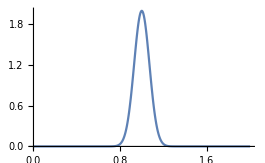

```mathematica
g[x_]=2 Exp[-((x-1)/.1)^2];Plot[g[x],{x,0,2},PlotRange->All]
```

### Function to initialize array given g(x) and dx

```mathematica
init=Function[{g,dx},g/@Range[0,2,dx]];
```

## Lax Wendroff (Richtmyer) scheme for advection

### Source: https://en.wikipedia.org/wiki/Lax–Wendroff_method

```mathematica
f[x_]=x^2/2;
```

```mathematica
up= 1/2(u[i+1]+u[i])-dt/(2dx)(f[u[i+1]]-f[u[i]]);
```

```mathematica
um= 1/2(u[i]+u[i-1])-dt/(2dx)(f[u[i]]-f[u[i-1]]);
```

### Update rule for LW Richtmyer scheme

```mathematica
rLWR=u[i]->u[i]-dt/dx(f[up]-f[um]);rLWR//TraditionalForm
```

u(i)→u(i)-1/dx dt (1/2 (1/2 (u(i)+u(i+1))-(dt (1/2 (u(i+1))^2-(u(i))^2/2))/(2 dx))^2-1/2 (1/2 (u(i-1)+u(i))-(dt ((u(i))^2/2-1/2 (u(i-1))^2))/(2 dx))^2)

### Simplifying RHS

```mathematica
exp1=rLWR[[2]]/.{u[i+1]->#3,u[i]->#2,u[i-1]->#1}//Simplify//InputForm
```

#2 - (dt*(-((2*dx + dt*(#1 - #2))^2*(#1 + #2)^2) + (2*dx + dt*(#2 - #3))^2*(#2 + #3)^2))/(32*dx^3)

### Function to advance by one time-step using LW Richtmyer method

```mathematica
LWR=Function[{v,dx,dt},ArrayPad[ArrayFilter[#2-(dt*(-((2*dx+dt*(#1-#2))^2*(#1+#2)^2)+(2*dx+dt*(#2-#3))^2*(#2+#3)^2))/(32*dx^3)&@@#&,v,1][[2;;-2]],1]];
```

## Alternate Lax-Wendroff scheme for advection

```mathematica
vjp=dt/dx 1/2(u[j+1]+u[j]);
```

```mathematica
hjp=1/2( 1/2u[j+1]^2+1/2u[j]^2-vjp(1/2u[j+1]^2-1/2u[j]^2));
```

```mathematica
vjm=dt/dx 1/2(u[j-1]+u[j]);
```

```mathematica
hjm= 1/2(1/2u[j-1]^2+1/2u[j]^2-vjm(1/2u[j]^2-1/2u[j-1]^2));
```

### Update rule for LW scheme

```mathematica
rLW=u[j]->u[j]-dt/dx(hjp-hjm);rLW//TraditionalForm
```

u(j)→u(j)-(dt (1/2 ((dt (u(j-1)+u(j)) ((u(j))^2/2-1/2 (u(j-1))^2))/(2 dx)-1/2 (u(j-1))^2-(u(j))^2/2)+1/2 (-(dt (u(j)+u(j+1)) (1/2 (u(j+1))^2-(u(j))^2/2))/(2 dx)+(u(j))^2/2+1/2 (u(j+1))^2)))/dx

### Simplifying RHS

```mathematica
exp2=rLW[[2]]/.{u[j+1]->#3,u[j]->#2,u[j-1]->#1}//FullSimplify
```

(8 dx^2 #2+2 dt dx (#1^2-#3^2)+dt^2 (#1^3+#1^2 #2-#1 #2^2-2 #2^3-#2^2 #3+#2 #3^2+#3^3))/(8 dx^2)

### Function to advance by one time-step using LW

```mathematica
LW=Function[{v,dx,dt},ArrayPad[ArrayFilter[(8*dx^2*#2+2*dt*dx*(#1^2-#3^2)+dt^2*(#1^3+#1^2*#2-#1*#2^2-2*#2^3-#2^2*#3+#2*#3^2+#3^3))/(8*dx^2)&@@#&,v,1][[2;;-2]],1]];
```

## Crank-Nicholson scheme for diffusion part

### Equation to solve to update by one time step ( u → v )

```mathematica
(u[i][n+1]-u[i][n])/dt-μ/2/dx^2(u[i+1][n+1]-2u[i][n+1]+u[i-1][n+1]+u[i+1][n]-2u[i][n]+u[i-1][n])==0/.{u[x_][n+1]->v[x],u[x_][n]->u[[x]]}//TraditionalForm//Quiet
```

(v(i)-u⟦i⟧)/dt-(μ (u⟦i-1⟧-2 u⟦i⟧+u⟦i+1⟧+v(i-1)-2 v(i)+v(i+1)))/(2 dx^2)==0

### Function to update by one time step using CN with built-in LinearSolve function

```mathematica
CN=Function[{u,dx,dt,μ},Module[{v,n},n=Length@u;v[1]=0;v[n]=0;
ArrayPad[LinearSolve[#[[2]],-#[[1]]]&@CoefficientArrays[Table[(-u[[i]]+v[i])/dt-(μ*(u[[-1+i]]-2*u[[i]]+u[[1+i]]+v[-1+i]-2*v[i]+v[1+i]))/(2*dx^2)==0,{i,2,n-1}],Table[v[i],{i,2,n-1}]],1]]];
```

### Faster function specifically for dx=0.02 and μ=0.01

```mathematica
sol[dt_]:=sol[dt]=LinearSolve[CoefficientArrays[Table[-25dt v[-1+i]+2 (1+25 dt) v[i]-25dt v[1+i]==25 dt u[-1+i]+2 (1-25 dt) u[i]+25dt u[1+i],{i,2,100}],Table[v[i],{i,2,100}]][[2]]];
```

```mathematica
fCN=
Function[{u,dx,dt,μ},ArrayPad[sol[dt]@(ArrayFilter[25dt #3+2(1-25dt)#2+25dt #1&@@#&,u,1][[2;;-2]]),1]];
```

## Combining both schemes using Godunov method

### Function to iterate upto one second given initial f(x), dx, dt, and μ

```mathematica
iterG=Function[{f,dx,dt,μ},NestWhileList[fCN[#,dx,dt,μ]&[LWR[#,dx,dt]]&,init[f,dx],Max@Abs@#<3.5&,1,Floor[1/ dt]]];
```

## Combining both schemes using Strang splitting

### Function to iterate upto one second given initial f(x), dx, dt, and μ

```mathematica
iterS=Function[{f,dx,dt,μ},NestWhileList[LWR[#,dx,1/2dt]&[fCN[#,dx,1/2dt,μ]&[fCN[#,dx,1/2dt,μ]&[LWR[#,dx,1/2dt]]]]&,init[f,dx],Max@Abs@#<3.5&,1,Floor[1/ dt]]];
```

## Plotting solutions with both methods at t=1 for dx=0.02, dt=0.01, and μ=0.01

```mathematica
With[{S=iterS[g,.02,.01,.01],G=iterG[g,.02,.01,.01]},Manipulate[ListLinePlot[Transpose[{Range[0,2,.02],#[[i]]}]&/@{G,S},PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"Godunov","Strang"}],{i,1,Length@S,1}]]
```

## Time step stability criterion

The maximum allowed timestep is determined by the CFL criterion for the Lax-Wendroff method:

Max[u]dt/dx ==1

Here maximum value of u is 2 from the given initial function. 
Therefore for dx=0.02 the maximum allowed value of dt is 0.01.

d)

## Range of time steps used

```mathematica
trange=.01 10^Range[-4,0]
```

{1.×10^-6,0.00001,0.0001,0.001,0.01}

## Computing solutions using Godunov method for different time steps

```mathematica
dataG=ParallelMap[iterG[g,.02,#,.01][[-1]]&,trange];//AbsoluteTiming
```

{3928.74,Null}

## Computing solutions using Strang splitting for different time steps

```mathematica
dataS=ParallelMap[iterS[g,.02,#,.01][[-1]]&,trange];//AbsoluteTiming
```

{7324.25,Null}

## Computing error

### Plotting error (L2 norm) for both methods vs step size

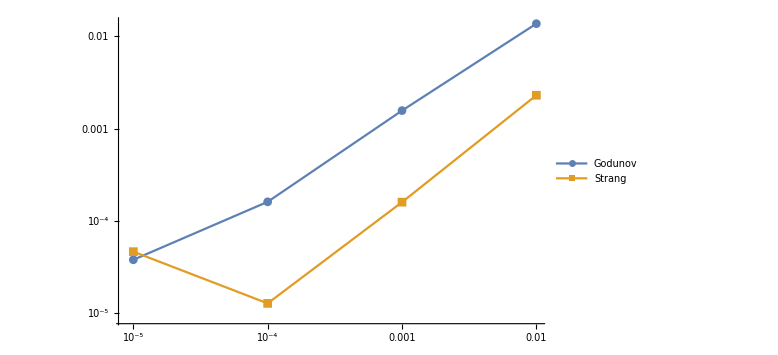

```mathematica
ListLogLogPlot[Function[d,Transpose[{trange[[2;;]],Norm[d[[1]]-d[[#]]]&/@Range[2,5]}]]/@{dataG,dataS},Joined->True,PlotMarkers->Automatic,PlotLegends->{"Godunov","Strang"},ImageSize->Large]
```

So in most cases, Strang Splitting seems to have steeper convergence as we have shown earlier (dt^3) compared to the Godunov method (which locally converges as dt^2).

## Q2

a)

Finite volume methods can be set up so that the fluxes leaving and entering each zone are exactly conserved. Therefore quantities that are supposed to be conserved remain conserved when using finite volume methods whereas this is not always the case for finite difference methods.

b)

The information takes O(n) steps to propagate from one end of the array to the opposite end for each wavenumber. Therefore it takes (O(n))^2 steps to converge.

c)

No idea. Wthout internet, I guess I’m not really much better than a caveman.

d)

When particles get too close to each other, the forces and potentials can become inifinitely large causing overflows. Also this can lead to all the particles converging to a single point. Therefore force softening is used to prevent this from happening.

e)

Riemann solvers are used to calculate the exact value of the fluxes at the cell boundaries.

f)

Verification means ensuring that the solutions to a mathematical model are correct. Validation means that the solution works to model the real world in some meaningful manner.

g)

Magnetohydrodynamics allows for more types of characterstics waves (around 7) compared to hydrodynamics (around 3).

h)

Latency and throughput are important for a parallel computer for achieving good parallel efficiency.

i)

No clue. Was in India during classes on radiation.

j)

Stiff equations require timesteps to be extremely small compared to the total time.